```mathematica
A=10000;
```

```mathematica
m=1/220;
```

```mathematica
a=0.1;
```

```mathematica
s=13000;
```

```mathematica
r=140;
```

```mathematica
f[x_] := 1/(1+m*x/A)
```

```mathematica
g[x_] := s/(1+a*x/A)
```

```mathematica
h[x_] := r/(1+a*x/A)
```

```mathematica
i[x_] := x*s/(1+a*x/A)
```

```mathematica
j[x_] := x*r/(1+a*x/A)
```

```mathematica
k[x_] := 1/(1+a*x/A)
```

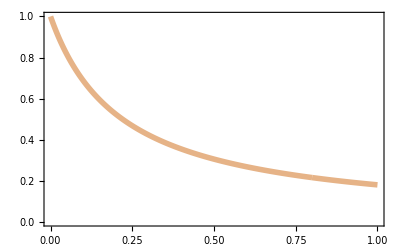

```mathematica
ListLinePlot[Table[{y,f[y]},{y,0,10000000,1000}],Joined->True,PlotStyle->Directive[Full,RGBColor["#E6B387"],Thickness[0.01]],Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->None]
```

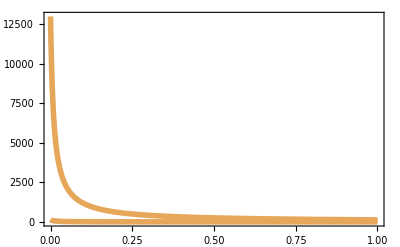

```mathematica
ListLinePlot[{Table[{y,g[y]},{y,0,10000000,1000}],Table[{y,h[y]},{y,0,10000000,1000}]},PlotRange->All,Joined->True,PlotStyle->Directive[Full,{RGBColor["#E68F5A"],RGBColor["#E6A75A"]},Thickness[0.01]],Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->None]
```

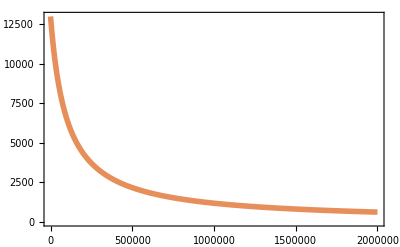

```mathematica
ListLinePlot[Table[{y,g[y]},{y,1,2000001,1000}],PlotRange->All, Joined->True,PlotStyle->Directive[Full,RGBColor["#E68F5A"],Thickness[0.01]],Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->None]
```

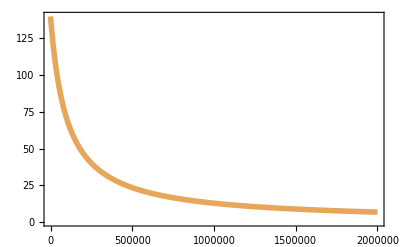

```mathematica
ListLinePlot[Table[{y,h[y]},{y,1,2000001,1000}],PlotRange->All, Joined->True,PlotStyle->Directive[Full,RGBColor["#E6A75A"],Thickness[0.01]],Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->None]
```

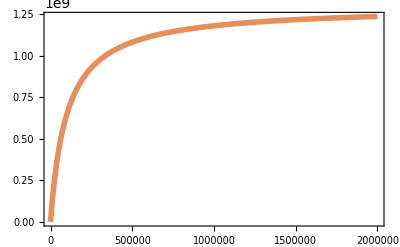

```mathematica
ListLinePlot[Table[{y,i[y]},{y,1,2000001,1000}],PlotRange->All, Joined->True,PlotStyle->Directive[Full,RGBColor["#E68F5A"],Thickness[0.01]],Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->None]
```

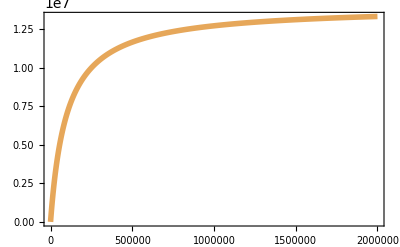

```mathematica
ListLinePlot[Table[{y,j[y]},{y,1,2000001,1000}],PlotRange->All, Joined->True,PlotStyle->Directive[Full,RGBColor["#E6A75A"],Thickness[0.01]],Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->None]
```

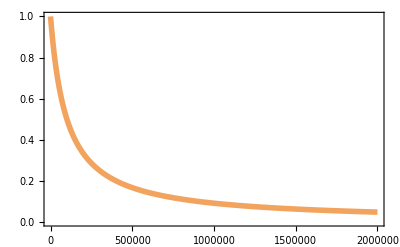

```mathematica
ListLinePlot[Table[{y,k[y]},{y,1,2000001,1000}],PlotRange->All, Joined->True,PlotStyle->Directive[Full,RGBColor["#F2A35E"],Thickness[0.01]],Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->None]
```